```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Distance Transforms

The distance transform replaces each pixel of an image by its distance from a specified set.

```mathematica
TableForm[{{Hyperlink["ManyDistances",{"visualVocabDistance.nb","labelManyDistances"}],labelManyDistances},{Hyperlink["ConnectedRegions",{"visualVocabDistance.nb","labelConnectedRegions"}],labelConnectedRegions},{Hyperlink["DistanceSkeleton",{"visualVocabDistance.nb","labelDistanceSkeleton"}],labelDistanceSkeleton}}]
```

| Comparison of three distances measures
 | The distance transform can help locate connected regions and aid in segmentation
 | The distance transform can be used to find the skeleton (the connected inner core) of a shape

The major function used in this notebook is DistanceTransform[ ] which carries out the needed calculations.

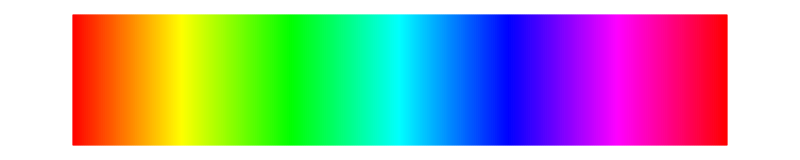

```mathematica
specLine
```

The first demonstration, by Henry Kwong, shows a set consisting of several yellow boxes. Each yellow box is marked "0" because points within the set are distance 0 from the set. Nearby points are labeled 1, 2, 3, etc. depending on the distance to the nearest point in the set. Click on the boxes to add (or remove) points from the set. There are three different notions of distance: the "city block distance", the square of the familiar Euclidean distance (this is squared so that all the numbers fit nicely in the grid) and a distance measure due to Chebyshev, sometimes called the “chessboard distance.” These are the kind of calculations that underly the distance transform.

```mathematica
labelManyDistances="Comparison of three distances measures";
infoManyDistances="The yellow squares define a set: the grid of values shows the distance from every point in the array to that set.\n\nClick on any point to make it part of the set. When the square turns yellow, it has distance zero (because points in the set have zero distance from the set). If a square is yellow and you click on it, it stops being part of the set and all distances are recalculated.\n\nThe chooser box allows selection of three different meanings of the word 'distance'.\n\nFind the largest distance you can for each of the three measures.";
distancetransformfunc[rasterData_List,distFun_]:=
Module[{nearestFn,xLen,yLen,featurePsns},{yLen,xLen}=Dimensions@rasterData;
featurePsns=Position[rasterData,1];
nearestFn=If[featurePsns==={},{∞}&,Nearest[featurePsns,DistanceFunction->distFun]];
Table[distFun[{y,x},First@nearestFn@{y,x}],{y,1,yLen},{x,xLen}]];
rasterData=Normal@SparseArray[{{3,3}->1,{7,6}->1},{9,9}];
Manipulate[
DynamicModule[{dtArr,togglePsn={0,0},x,y},
{x,y}=Dimensions@localRasterData;
dtArr=distancetransformfunc[localRasterData,distFun];
Dynamic@(
If[togglePsn=={0,0},{},localRasterData=ReplacePart[localRasterData,
togglePsn->Mod[Extract[localRasterData,togglePsn]+1,2]];
togglePsn={0,0}];
Pane[TableForm[MapIndexed[
Button[Extract[dtArr,#2],togglePsn=#2,ImageSize->{350/(x+1),350/(y+1)},Background->{LightGray,RGBColor[1, 0.8, 0]}[[1+#1]]]&,
localRasterData,{2}]],{400,400},Alignment->Center])],
Row[{Control[{{distFun,ManhattanDistance,"distance measure"},{ManhattanDistance->"Manhattan",SquaredEuclideanDistance->"Squared Euclidean",ChessboardDistance->"Chessboard"}}],Spacer[20],info[infoManyDistances]}],
{{localRasterData,rasterData},ControlType->None},
FrameLabel->Style[labelManyDistances,Medium],TrackedSymbols->{localRasterData,distFun},SaveDefinitions->True]
```

The Euclidean distance is the normal distance between two points as one might measure with a ruler. The chessboard distance is the number of steps it would take a (chess) king to move from the current location to the set. The city-block distance

```mathematica
specLine
```

-Graphics-

Calculating the distance transform for an image is as simple as calling DistanceTransform[ ]. The first argument is an image and the second argument is a threshold value used to define the background set (the set to which all distances are calculated). Here is a somewhat blotchy blue and white image (it is the result of a majority rules cellular automata, but this is irrelevant for the purposes of the present discussion). The distance transform is applied twice, once calculating the distance from every point to the white region and once calculating the distance from every point to the blue region. Both show a skeleton-like structure that indicates the strength of the connectedness of the regions.

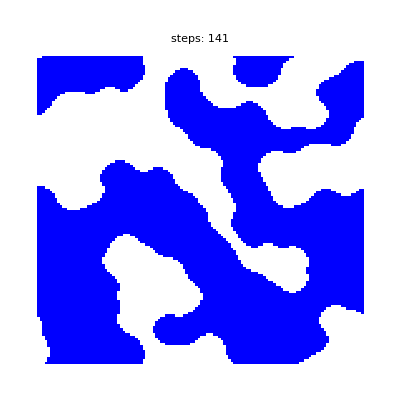
```mathematica
img=-Graphics-; bwMat=ImageData[ColorConvert[img,"GrayScale"]];
```

```mathematica
Labeled[GraphicsRow[{ImageAdjust[DistanceTransform[Image[1-bwMat],0.6]],ImageAdjust[DistanceTransform[Image[bwMat],0.3]]},ImageSize->600],"The internal and external skeletons reveal the connectivity within the image",LabelStyle->captionStyle]
```

-Graphics-The internal and external skeletons reveal the connectivity within the image

The distance transform can help to locate connected regions in an image. Applying a high pass filter after the distancing operation can often bring out the edges in the image and aid in segmentation.

```mathematica
labelConnectedRegions="The distance transform can help locate connected regions and aid in segmentation";
infoConnectedRegions="The distance transform applied to binarized thread x-rays. Using any of the three distance functions, the distance transform shows how close the nearest of the black point is. When objects are small, this creates many small features.\n\nFor example, with image F634Tile (negative, threshold=0.43) only the peaks of the threads are visible. Clicking the high pass option emphasizes these even more.\n\nLookong at L11 (positive, threshold 0.63), the staple is clearly visible.";
Manipulate[
If[invert=="negative",imgD=allImagesXray[[i]],imgD=ColorNegate[allImagesXray[[i]]]];dtImg=ImageAdjust[DistanceTransform[imgD,s,DistanceFunction->distFun]];
dtFiltImg=ImageAdjust[ColorNegate[LaplacianGaussianFilter[dtImg,2]]];
If[filt,dtFiltImg,dtImg],
Row[{Control[{{i,3,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20]Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoConnectedRegions]}],
{{distFun,EuclideanDistance,"distance function"},{EuclideanDistance->"Euclidean",ManhattanDistance->"Manhattan",ChessboardDistance->"Chessboard"}},{{s,0.2,"threshold"},0.0,0.7},{{filt,False,"high pass filter"},{True,False}},
FrameLabel->Style[labelConnectedRegions,Medium],TrackedSymbols->{i,distFun,s,filt,invert},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesXray⟦3⟧ is longer than depth of object.

DistanceTransform::imginv: Expecting an image or graphics instead of allImagesXray⟦3⟧.

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[allImagesXray⟦3⟧,0.2,DistanceFunction→EuclideanDistance].

LaplacianGaussianFilter::arg1: The first argument ImageAdjust[DistanceTransform[allImagesXray⟦3⟧,0.2,DistanceFunction→EuclideanDistance]] is neither a rectangular array nor an image.

ColorNegate::imginv: LaplacianGaussianFilter[ImageAdjust[DistanceTransform[allImagesXray⟦3⟧,0.2,DistanceFunction→EuclideanDistance]],2] should be a valid image, a color directive, or a list of such objects.

ImageAdjust::imginv: Expecting an image or graphics instead of ColorNegate[LaplacianGaussianFilter[ImageAdjust[DistanceTransform[allImagesXray⟦3⟧,0.2,DistanceFunction→EuclideanDistance]],2]].

Part::partd: Part specification allImagesXray⟦3⟧ is longer than depth of object.

DistanceTransform::imginv: Expecting an image or graphics instead of allImagesXray⟦3⟧.

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[allImagesXray⟦3⟧,0.2,DistanceFunction→EuclideanDistance].

LaplacianGaussianFilter::arg1: The first argument ImageAdjust[DistanceTransform[allImagesXray⟦3⟧,0.2,DistanceFunction→EuclideanDistance]] is neither a rectangular array nor an image.

ColorNegate::imginv: LaplacianGaussianFilter[ImageAdjust[DistanceTransform[allImagesXray⟦3⟧,0.2,DistanceFunction→EuclideanDistance]],2] should be a valid image, a color directive, or a list of such objects.

ImageAdjust::imginv: Expecting an image or graphics instead of ColorNegate[LaplacianGaussianFilter[ImageAdjust[DistanceTransform[allImagesXray⟦3⟧,0.2,DistanceFunction→EuclideanDistance]],2]].

```mathematica
specLine
```

-Graphics-

The distance transform can also be a useful component of a skeleton-finding algorithm.

```mathematica
labelDistanceSkeleton="The distance transform can be used to find the skeleton (the connected inner core) of a shape";infoDistanceSkeleton="For simple shapes, the distance transform has a simple intrepretation: the further from a boundary a point is, the whiter the point.\n\nIn the first image (upper left), the brightest spot is the one furthest from the border, which is at the center of the largest triangular shape (upper right). Thinning this (pruning to contain only the ridges) leads to the two bottom images, one thinning the image and one thinning the distance transform. They contain similar information.\n\nChoose different shapes from the popup menu and examine the distance transform and the skeletons.";
Manipulate[GraphicsGrid[{{img=ColorNegate[shapes[[i]]],imgDist=ImageAdjust[DistanceTransform[img]]},{Thinning[img],Dilation[Thinning[imgDist],1]}},ImageSize->600],Row[{Control[{{i,1,"image"},Thread[Range[Length[shapes]]->shapes],ControlType->PopupMenu}],Spacer[20],info[infoDistanceSkeleton]}],FrameLabel->Style[labelDistanceSkeleton,Medium],TrackedSymbols->{i},SaveDefinitions->saveDef]
```

Part::partd: Part specification shapes⟦1⟧ is longer than depth of object.

ColorNegate::imginv: shapes⟦1⟧ should be a valid image, a color directive, or a list of such objects.

DistanceTransform::imginv: Expecting an image or graphics instead of ColorNegate[shapes⟦1⟧].

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[ColorNegate[shapes⟦1⟧]].

Thinning::labimginv: ColorNegate[shapes⟦1⟧] is not a valid image nor label matrix.

Thinning::labimginv: ImageAdjust[DistanceTransform[ColorNegate[shapes⟦1⟧]]] is not a valid image nor label matrix.

Dilation::arg1: The first argument Thinning[ImageAdjust[DistanceTransform[ColorNegate[shapes⟦1⟧]]]] is neither a rectangular array nor an image.

Part::partd: Part specification shapes⟦1⟧ is longer than depth of object.

ColorNegate::imginv: shapes⟦1⟧ should be a valid image, a color directive, or a list of such objects.

DistanceTransform::imginv: Expecting an image or graphics instead of ColorNegate[shapes⟦1⟧].

ImageAdjust::imginv: Expecting an image or graphics instead of DistanceTransform[ColorNegate[shapes⟦1⟧]].

Thinning::labimginv: ColorNegate[shapes⟦1⟧] is not a valid image nor label matrix.

Thinning::labimginv: ImageAdjust[DistanceTransform[ColorNegate[shapes⟦1⟧]]] is not a valid image nor label matrix.

Dilation::arg1: The first argument Thinning[ImageAdjust[DistanceTransform[ColorNegate[shapes⟦1⟧]]]] is neither a rectangular array nor an image.